## Define Mueller Matrices

#### According to a Chp 22 in an optics handbook (chapter authored by Russell A. Chipman), We have the following mueller matrix for a general retarder

```mathematica
MuellerRotation[theta1].LRzero[delta1].Transpose[MuellerRotation[theta1]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[2 theta1]^2+Cos[delta1] Sin[2 theta1]^2 | Cos[2 theta1] Sin[2 theta1]-Cos[delta1] Cos[2 theta1] Sin[2 theta1] | -Sin[delta1] Sin[2 theta1]
0 | Cos[2 theta1] Sin[2 theta1]-Cos[delta1] Cos[2 theta1] Sin[2 theta1] | Cos[delta1] Cos[2 theta1]^2+Sin[2 theta1]^2 | Cos[2 theta1] Sin[delta1]
0 | Sin[delta1] Sin[2 theta1] | -Cos[2 theta1] Sin[delta1] | Cos[delta1])

```mathematica
"
```

```mathematica
(*General Retarder*)
LR[θfast_,retardance_]:=({{1, 0, 0, 0}, {0, Cos[2θfast]^2+Sin[2θfast]^2 Cos[2π retardance], Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), -Sin[2θfast]Sin[2π retardance]}, {0, Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), Sin[2θfast]^2+Cos[2θfast]Cos[2π retardance]^2, Cos[2 θfast]Sin[2π retardance]}, {0, Sin[2θfast]Sin[2π retardance], -Cos[2 θfast]Sin[2π retardance], Cos[2π retardance]}})
(* Retarder at 0 degrees *)
LRzero[δ_]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[δ], Sin[δ]}, {0, 0, -Sin[δ], Cos[δ]}});
(* Linear Polarizer at 0 with  k value *)
LPzeroWithK[δ_,k1_]:=1/2({{1, k1, 0, 0}, {k1, 1, 0, 0}, {0, 0, √(1-k1^2), 0}, {0, 0, 0, √(1-k1^2)}});
(* Perfect linear polarizer *)
LPzero=1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
(* We can rotate optical elements and input polarization with the following matrix *)
	MuellerRotation[θ_]:=({{1, 0, 0, 0}, {0, Cos[2θ], -Sin[2θ], 0}, {0, Sin[2θ], Cos[2θ], 0}, {0, 0, 0, 1}});
(* An optical element at an arbitrary angle can be obtained by rotating the matrix. Since it's a matrix we're rotating and not a vector,
	we must multiply by the matrix and the transpose, like so *)
LP[θ_]:=MuellerRotation[θ].LPzero.Transpose[MuellerRotation[θ]]
```

## Play Around with them

## We will assume our incident vector was 100% linearly polarized in the horizontal direction

```mathematica
inc=({{1}, {1}, {0}, {0}});
```

## First, we pass the light through a horizontal linear polarizer and a vertical linear polarizer.

### First Horizontal

```mathematica
LPzero.inc
```

{{1},{1},{0},{0}}

The stokes vector is unaffected, as we would expect.

### Then vertical

```mathematica
vertLP=MuellerRotation[π/2].LPzero.Transpose[MuellerRotation[π/2]];
MatrixForm[vertLP.inc]
```

(0
0
0
0)

The stokes vector is completely extinguished, as we would expect.

### Now we want to have an arbitrary linearly polarized input, and see how the intensity changes as the angle changes for both the vertical polarizer and the horizontal polarizer. We begin the arbitrary polarization at 45°.

```mathematica
(* We start with a horizontally polarized stokes vector. *)
inc=({{1}, {1}, {0}, {0}});
(* We can define the linear polarizer at an arbitrary angle by rotating the LP that is at zero.*)
arbLP[θ_]:=MuellerRotation[θ].LPzero.Transpose[MuellerRotation[θ]];

(* We can define an arbitrary linearly polarized stokes vector by rotating the stokes vector itself. *)
arbinc=MuellerRotation[θ].inc;

(* Here we can see the equation the governs the arbitrary input *)
MatrixForm[arbinc]

(* Here we evaluate the arbitrary input to a specific angle using a replacement rule *)
MatrixForm[arbinc/.θ->π/4]
```

(1
Cos[2 θ]
Sin[2 θ]
0)

(1
0
1
0)

## Simulating Polarimeter Data

```mathematica
tickM=Range[0,2π,π/2];
```

{0,π/2,π,(3 π)/2,2 π}

```mathematica
(* Import the package to analyze the simulated data. *)
SetDirectory[$PACKAGES]
Import["polarization.wl"]
```

C:\Users\karla\Box Sync\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\packages

1

RandomGeneratorState[…]

92

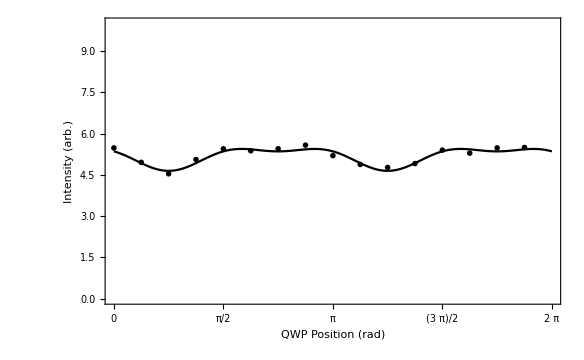

```mathematica
p0=10;
p1=1/Sqrt[2]/10;
p2=0;
p3=1/Sqrt[2]/10;

alpha=0;

beta=68.7*π/180*0;
beta=0;
counts=1000;
noiseMultiplier=0;
currentNoise=0;
retard=.25*2*π;

inc=({{p0}, {p1}, {p2}, {p3}}); (* Stokes vector to simulate *)

inc=UnNormalizeStokes[inc];
pl=Plot[{(LP[alpha*π/180].MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]},{θ,0,2π},AxesOrigin->{0,0},ImageSize->{720,450},PlotStyle->colorBlindPalette[[1]],PlotRange->{0,10}];

noiseMultiplier=1

PolarimeterDataGenerator[angle_]:=(LP[alpha].MuellerRotation[angle].LRzero[retard].Transpose[MuellerRotation[angle]].inc)[[1]][[1]];
angles=Range[0,2π,2π/16];
angles=angles[[;;-2]];
SeedRandom[]
seeder=RandomInteger[{0,99}];
seeder=92
seeds=Range[0,Length[angles]];
polData={};
For[i=1,i≤Length[angles],i++,
SeedRandom[seeder+seeds[[i]]];
noise=(currentNoise+Sqrt[counts]/counts*noiseMultiplier)*p0*RandomReal[{-1/2,1/2}];
AppendTo[polData,PolarimeterDataGenerator[angles[[i]]]+noise];
]
plotData=Transpose[{angles,polData}];

p=Show[{ListPlot[{plotData},PlotRange->{0,10},PlotStyle->colorBlindPalette],pl},FrameLabel->{"QWP Position (rad)","Intensity (arb.)"},PlotRange->{0,10},polarimeterPlotOptions,PlotRange->{0,10}]
```

<|Sin Coefficients→<|0→0.,1→0.0171402,2→-0.373663,3→-0.0217528,4→-0.0680698,5→0.0361966,6→0.0310176,7→0.0258546|>,Cos Coefficients→<|0→5.20604,1→0.0191999,2→0.00367981,3→0.0445949,4→0.160534,5→0.0597719,6→-0.0452048,7→0.0077506|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>

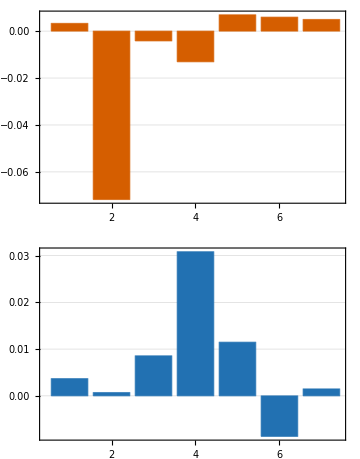

```mathematica
fc=DFT[polData]
fcg=FourierCoefficientBarChart[fc];
fcgg=GraphicsGrid[{{fcg[[1]]},{fcg[[2]]}},ImageSize->Medium]
```

```mathematica
s=fc["Sin Coefficients"];
c=fc["Cos Coefficients"];
beta=0;
stokes=CalculateStokesFromFourierCoefficients[c[0],c[2],c[4],s[2],s[4],1,0,0,π/2]
stokesV=MatrixForm[Transpose[{Chop[stokes//Values,10^-5]}]]
```

<|p0→5.,p1→0.707107,p2→0.,p3→0.707107|>

(5.
0.707107
0
0.707107)

{1/2+1/2 Cos[2 θ]^2-(0.-3.06162×10^-17 Sin[2 θ]) Sin[2 θ]}

RGBColor[Rational[2, 15], Rational[113, 255], Rational[178, 255]]

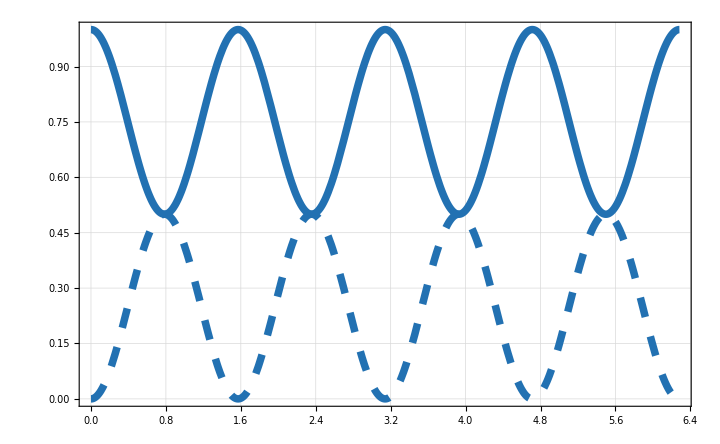

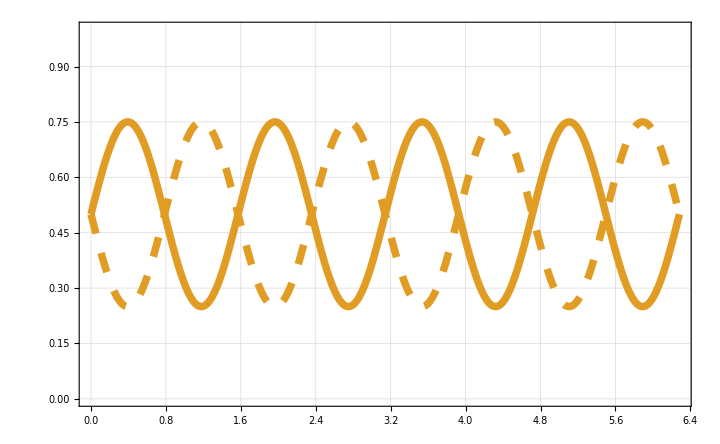

{0.5-0.5 Sin[2 θ]}

{0.5+0.5 Sin[2 θ]}

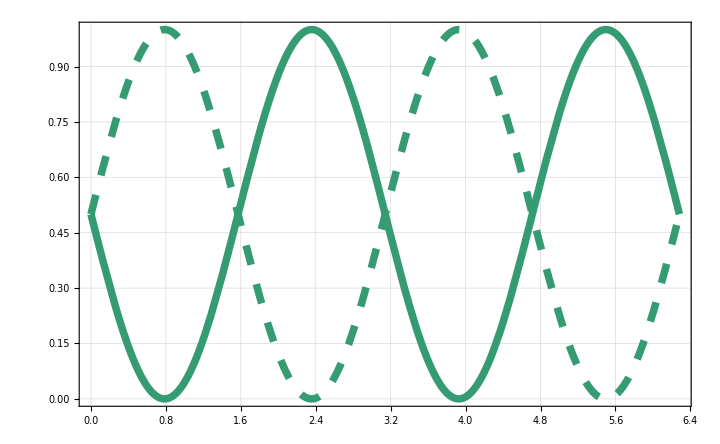

```mathematica
inc=({{1}, {1}, {0}, {0}});

retard=.25*2π;
horizontal=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]

inc=({{1}, {-1}, {0}, {0}});
blue=colorBlindPalette[[3]]
color=blue;
thickness=.0075;
dashThick1=.02;
dashThick2=.02;
vertical=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
Plot[{horizontal,vertical},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1}]

inc=({{1}, {0}, {1}, {0}});
plus45=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
inc=({{1}, {0}, {-1}, {0}});
orange=ColorData[97,"ColorList"][[2]];
color=orange;
minus45=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
Plot[{plus45,minus45},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1}]
inc=({{1}, {0}, {0}, {1}});
rcp=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]
inc=({{1}, {0}, {0}, {-1}});
green=colorBlindPalette[[4]];
color=green;
lcp=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]
Plot[{rcp,lcp},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1}]
```

## Keith

```mathematica
result=LPzero.LRzero[r1].LR[θ,r2].LPzero.({{Io}, {Mo}, {Co}, {So}})
```

{{Co k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-k1 √(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))+Io (1+k1^2 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{Co √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-√(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1^2+Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2)+Io (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{√(1-k1^2) So (√(1-k1^2) Cos[2 π r2] Sin[r1]+√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2])+Io k1 (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Mo (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2]+√(1-k1^2) Cos[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2))},{√(1-k1^2) So (√(1-k1^2) Cos[r1] Cos[2 π r2]-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2])+Io k1 (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Mo (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2]-√(1-k1^2) Sin[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2))}}

```mathematica
MatrixForm[result]
```

(Co k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-k1 √(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))+Io (1+k1^2 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))
Co √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-√(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1^2+Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2)+Io (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))
√(1-k1^2) So (√(1-k1^2) Cos[2 π r2] Sin[r1]+√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2])+Io k1 (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Mo (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2]+√(1-k1^2) Cos[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2))
√(1-k1^2) So (√(1-k1^2) Cos[r1] Cos[2 π r2]-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2])+Io k1 (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Mo (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2]-√(1-k1^2) Sin[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2)))

```mathematica
result=LPzero.LR[θ,r2].LPzero.({{Io}, {Mo}, {Co}, {So}})
```

{{Co k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-k1 √(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))+Io (1+k1^2 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{Co √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-√(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1^2+Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2)+Io (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{(1-k1^2) So Cos[2 θ] Sin[2 π r2]+Io k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Mo (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+Co (1-k1^2) (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2)},{(1-k1^2) So Cos[2 π r2]-Co (1-k1^2) Cos[2 θ] Sin[2 π r2]+Io k1 √(1-k1^2) Sin[2 π r2] Sin[2 θ]+√(1-k1^2) Mo Sin[2 π r2] Sin[2 θ]}}

## 2021-03-24: Polarimeter Evaluation

```mathematica
inc=({{1}, {1}, {0}, {0}});

retard=.25*2π;
shift=-4.31;
θlpa =(20.4+shift)*π/180;
βo=(68.7+shift)*π/180;
θlpa =0*π/180;
βo=0*π/180;
horizontal=(MuellerRotation[θlpa].LPzero.Transpose[MuellerRotation[θlpa]].MuellerRotation[θ+βo].LRzero[retard].Transpose[MuellerRotation[θ+βo]].inc)[[1]]

inc=({{1}, {-1}, {0}, {0}});
blue=colorBlindPalette[[3]]
color=blue;
thickness=.0075;
dashThick1=.02;
dashThick2=.02;
vertical=(MuellerRotation[θlpa].LPzero.Transpose[MuellerRotation[θlpa]].MuellerRotation[θ+βo].LRzero[retard].Transpose[MuellerRotation[θ+βo]].inc)[[1]];
Clear[θ]
Plot[{horizontal,vertical},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1}]
```

{1/2+1/2 Cos[2 θ]^2-(0.-3.06162×10^-17 Sin[2 θ]) Sin[2 θ]}

RGBColor[Rational[2, 15], Rational[113, 255], Rational[178, 255]]

-Graphics-

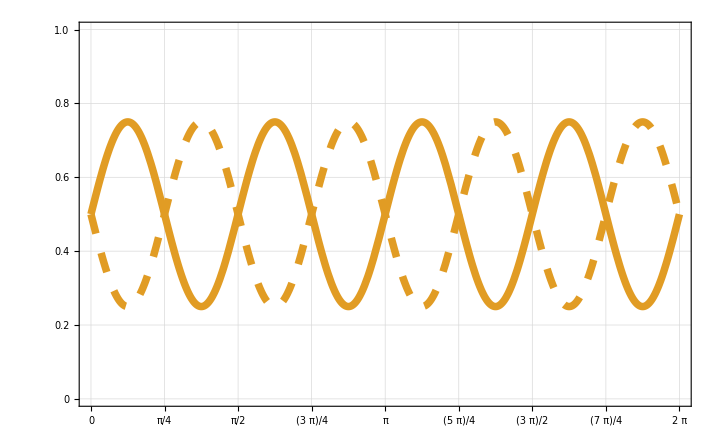

{0.5-0.5 Sin[2 θ]}

{0.5+0.5 Sin[2 θ]}

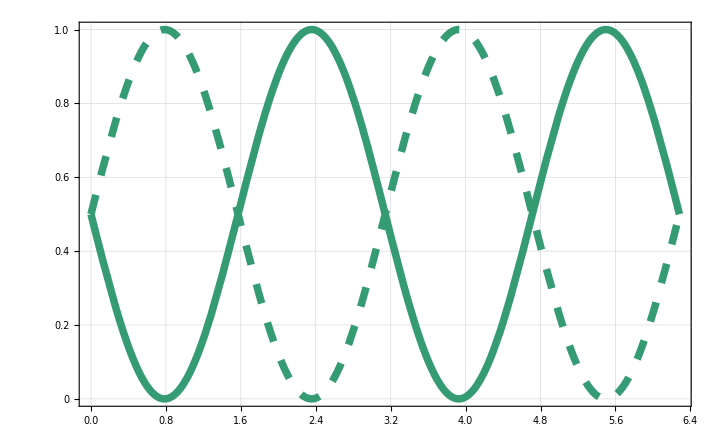

```mathematica
inc=({{1}, {0}, {1}, {0}});
plus45=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
inc=({{1}, {0}, {-1}, {0}});
orange=ColorData[97,"ColorList"][[2]];
color=orange;
minus45=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
Plot[{plus45,minus45},{θ,0,2π},
PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},
AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1},
FrameTicks->{{All,None},{Range[0,2π,π/4],None}}]
inc=({{1}, {0}, {0}, {1}});
rcp=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]
inc=({{1}, {0}, {0}, {-1}});
green=colorBlindPalette[[4]];
color=green;
lcp=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]
Plot[{rcp,lcp},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1},FrameTicks->{{All,None},{None,None}}]
```

```mathematica
(MuellerRotation[θlpa].LPzero.Transpose[MuellerRotation[θlpa]].MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]][[1]]
```

1/2+(0.+6.12323×10^-17 (1/4 √3 Cos[2 θ]-1/4 Sin[2 θ])) Sin[2 θ]-Cos[2 θ] (1/4 Cos[2 θ]+1/4 √3 Sin[2 θ])

{{1},{0.04},{0},{0}}

-0.441428

-0.681034

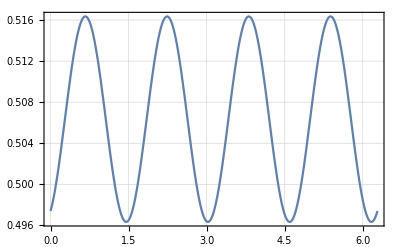

horizontal

```mathematica
inc=({{1}, {.04}, {0}, {0}})
alpha=alpha20210329*Pi/180
beta=beta20210329labFrame*Pi/180
Plot[(MuellerRotation[alpha].LPzero.Transpose[MuellerRotation[alpha]].MuellerRotation[(θ-beta)].LRzero[retard].Transpose[MuellerRotation[(θ-beta)]].inc)[[1]][[1]],{θ,0,2π}]
N[horizontal]
```

## My Polarimeter Simulator

## Just Linear Polarizer (Malus’ Law)

```mathematica
inc=({{1}, {1}, {0}, {0}});
```

```mathematica
LPzero.inc
```

{{1},{1},{0},{0}}

Rotating the LP to block the incident light.

```mathematica
th=π/2;
MuellerRotation[th].LPzero.Transpose[MuellerRotation[th]].inc
```

{{0},{0},{0},{0}}

Rotating the LP to generate +45 degree azimuthal vibration.

```mathematica
th=π/4;
MuellerRotation[th].LPzero.Transpose[MuellerRotation[th]].inc
```

{{1/2},{0},{1/2},{0}}

And -45 rotation gives the opposite sign.

```mathematica
th=-π/4;
MuellerRotation[th].LPzero.Transpose[MuellerRotation[th]].inc
```

{{1/2},{0},{-1/2},{0}}

An initially unpolarized light source will work too.

```mathematica
incUn=({{1}, {0}, {0}, {0}});
MuellerRotation[th].LPzero.Transpose[MuellerRotation[th]].incUn
```

{{1/2},{0},{-1/2},{0}}

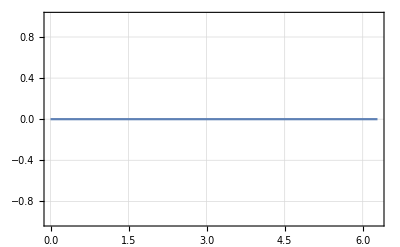

```mathematica
inc=({{1}, {1}, {0}, {0}});
th=90*Pi/180;
Plot[((MuellerRotation[anal].LPzero.Transpose[MuellerRotation[anal]]).(MuellerRotation[th].LPzero.Transpose[MuellerRotation[th]]).inc)[[1]],{anal,0,2π}]
```

## The Polarimeter

```mathematica
inc=({{1}, {0}, {0}, {0}});
alpha =0;
beta0=0;
delta=π/2;
MuellerRotation[alpha].LPzero.Transpose[MuellerRotation[alpha]].MuellerRotation[beta].LRzero[delta].Transpose[MuellerRotation[beta]].inc
```

{{1/2},{1/2},{0},{0}}

```mathematica
PlotPolarimeter[inc_List,alpha_,beta0_,delta_]:=Plot[(MuellerRotation[alpha].LPzero.Transpose[MuellerRotation[alpha]].MuellerRotation[beta0+beta].LRzero[delta].Transpose[MuellerRotation[beta0+beta]].inc)[[1]],{beta,0,2Pi}];
```

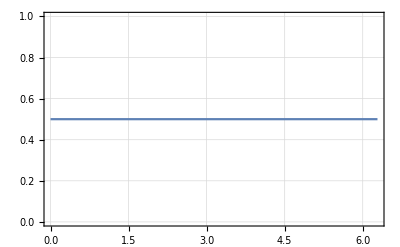

```mathematica
PlotPolarimeter[{{1},{0},{0},{0}},0,0,Pi/2]
```

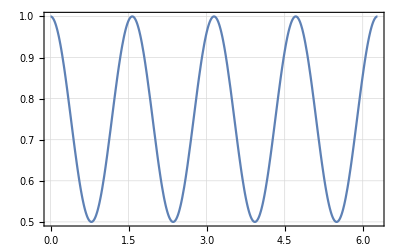

```mathematica
PlotPolarimeter[{{1},{1},{0},{0}},0,0,Pi/2]
```

And we also want to be able to generate data that we can then analyze with my mathematica program, hence this second function which gives discrete data points.

```mathematica
PolarimeterDataPoint[inc_List,alpha_,beta0_,delta_,beta_]:=N[(MuellerRotation[alpha].LPzero.Transpose[MuellerRotation[alpha]].MuellerRotation[beta0+beta].LRzero[delta].Transpose[MuellerRotation[beta0+beta]].inc)[[1]][[1]]];
```

{1.,0.978386,0.917283,0.827254,0.723868,0.625,0.547746,0.505463,0.505463,0.547746,0.625,0.723868,0.827254,0.917283,0.978386,1.,0.978386,0.917283,0.827254,0.723868,0.625,0.547746,0.505463,0.505463,0.547746,0.625,0.723868,0.827254,0.917283,0.978386,1.,0.978386,0.917283,0.827254,0.723868,0.625,0.547746,0.505463,0.505463,0.547746,0.625,0.723868,0.827254,0.917283,0.978386,1.,0.978386,0.917283,0.827254,0.723868,0.625,0.547746,0.505463,0.505463,0.547746,0.625,0.723868,0.827254,0.917283,0.978386,1.}

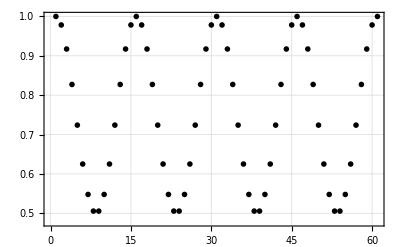

```mathematica
dataPoints=60;
pos=Range[0,2Pi,2Pi/dataPoints];
op=PolarimeterDataPoint[{{1},{1},{0},{0}},0,0,Pi/2,#]&/@pos
ListPlot[{op}]
```

Really, I think this is the above is the most important piece. This needs to be fed through my analysis program to see if I can extract out the input polarization vectors for known alpha and beta. Yet, I want to continue with my plan of attack and implement the retro reflection optical train.

```mathematica
PlotRetroReflection[inc_List,alpha_,beta0_,delta_]:=Plot[
(
MuellerRotation[alpha].LPzero.Transpose[MuellerRotation[alpha]].
MuellerRotation[beta0+beta].LRzero[delta].Transpose[MuellerRotation[beta0+beta]].
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}).
MuellerRotation[-(beta0+beta)].LRzero[delta].Transpose[MuellerRotation[-(beta0+beta)]].
MuellerRotation[-alpha].LPzero.Transpose[MuellerRotation[-alpha]].
inc)[[1]],{beta,0,2Pi}];
```

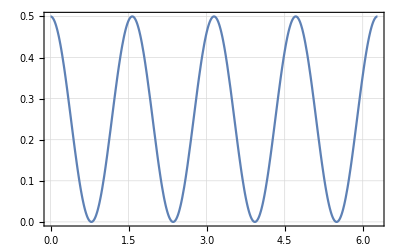

```mathematica
PlotRetroReflection[{{1},{0},{0},{0}},0,0,Pi/2]
```

## Now we need to verify that my analysis program correctly identifies the input polarization.

Here’s some linear horizontal light data

{1000.,750.,500.,750.,1000.,750.,500.,750.,1000.,750.,500.,750.,1000.,750.,500.,750.}

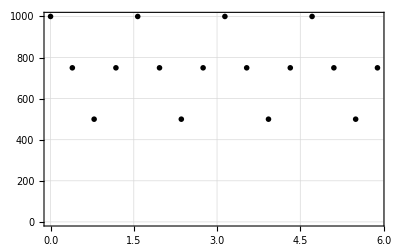

```mathematica
dataPoints=16;
pos=Range[0,2Pi-2Pi/dataPoints,2Pi/dataPoints];
intensity=PolarimeterDataPoint[{{1000},{1000},{0},{0}},0,0,Pi/2,#]&/@pos
op=Partition[Riffle[pos,intensity],2];
ListPlot[{op}]
```

```mathematica
intensity=Map[Around[#,Sqrt[#]]&, intensity]
```

{1000.32.,750.27.,500.22.,750.27.,1000.32.,750.27.,500.22.,750.27.,1000.32.,750.27.,500.22.,750.27.,1000.32.,750.27.,500.22.,750.27.}

```mathematica
DFT[intensity]
```

<|Sin Coefficients→<|0→0.,1→0.10.,2→0.9.,3→0.10.,4→0.10.,5→0.10.,6→0.9.,7→0.10.,8→0.|>,Cos Coefficients→<|0→750.7.,1→0.10.,2→0.10.,3→0.10.,4→250.10.,5→0.10.,6→0.10.,7→0.10.,8→0.7.|>|>

```mathematica
CalculateStokesFromDFT[DFT[intensity],1,0,0,π/2]
```

<|p0→500.12.,p1→1.000.05,p2→0.000.04,p3→0.0000.018|>

Here’s some linear vertical light data

{0.,250.,500.,250.,0.,250.,500.,250.,0.,250.,500.,250.,0.,250.,500.,250.}

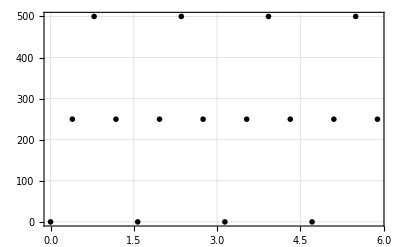

```mathematica
dataPoints=16;
pos=Range[0,2Pi-2Pi/dataPoints,2Pi/dataPoints];
intensity=PolarimeterDataPoint[{{1000},{-1000},{0},{0}},0,0,Pi/2,#]&/@pos
op=Partition[Riffle[pos,intensity],2];
ListPlot[{op}]
```

```mathematica
intensity=Map[Around[#,Sqrt[#]]&, intensity]
```

{0.,250.16.,500.22.,250.16.,0.,250.16.,500.22.,250.16.,0.,250.16.,500.22.,250.16.,0.,250.16.,500.22.,250.16.}

```mathematica
DFT[intensity]
```

<|Sin Coefficients→<|0→0.,1→0.6.,2→0.7.,3→0.6.,4→0.6.,5→0.6.,6→0.7.,7→0.6.,8→0.|>,Cos Coefficients→<|0→250.4.,1→0.6.,2→0.4.,3→0.6.,4→-250.6.,5→0.6.,6→0.4.,7→0.6.,8→0.4.|>|>

```mathematica
CalculateStokesFromDFT[DFT[intensity],1,0,0,π/2]
```

<|p0→500.7.,p1→-1.0000.026,p2→0.0000.022,p3→0.0000.014|>

Here’s some linear +45 light data

{500.,750.,500.,250.,500.,750.,500.,250.,500.,750.,500.,250.,500.,750.,500.,250.}

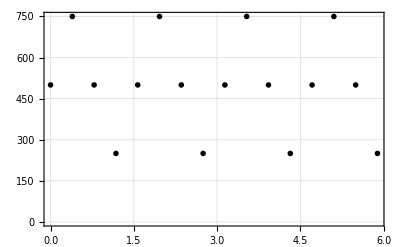

```mathematica
dataPoints=16;
pos=Range[0,2Pi-2Pi/dataPoints,2Pi/dataPoints];
intensity=PolarimeterDataPoint[{{1000},{0},{1000},{0}},0,0,Pi/2,#]&/@pos
op=Partition[Riffle[pos,intensity],2];
ListPlot[{op}]
```

```mathematica
intensity=Map[Around[#,Sqrt[#]]&, intensity]
```

{500.22.,750.27.,500.22.,250.16.,500.22.,750.27.,500.22.,250.16.,500.22.,750.27.,500.22.,250.16.,500.22.,750.27.,500.22.,250.16.}

```mathematica
DFT[intensity]
```

<|Sin Coefficients→<|0→0.,1→0.8.,2→0.8.,3→0.8.,4→250.8.,5→0.8.,6→0.8.,7→0.8.,8→0.|>,Cos Coefficients→<|0→500.6.,1→0.8.,2→0.8.,3→0.8.,4→0.8.,5→0.8.,6→0.8.,7→0.8.,8→0.6.|>|>

```mathematica
CalculateStokesFromDFT[DFT[intensity],1,0,0,π/2]
```

<|p0→500.10.,p1→0.0000.032,p2→1.000.04,p3→0.0000.016|>

Here’s some linear -45 light data

{500.,250.,500.,750.,500.,250.,500.,750.,500.,250.,500.,750.,500.,250.,500.,750.}

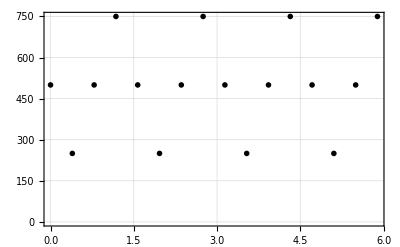

```mathematica
dataPoints=16;
pos=Range[0,2Pi-2Pi/dataPoints,2Pi/dataPoints];
intensity=PolarimeterDataPoint[{{1000},{0},{-1000},{0}},0,0,Pi/2,#]&/@pos
op=Partition[Riffle[pos,intensity],2];
ListPlot[{op}]
```

```mathematica
intensity=Map[Around[#,Sqrt[#]]&, intensity]
```

{500.22.,250.16.,500.22.,750.27.,500.22.,250.16.,500.22.,750.27.,500.22.,250.16.,500.22.,750.27.,500.22.,250.16.,500.22.,750.27.}

```mathematica
DFT[intensity]
```

<|Sin Coefficients→<|0→0.,1→0.8.,2→0.8.,3→0.8.,4→-250.8.,5→0.8.,6→0.8.,7→0.8.,8→0.|>,Cos Coefficients→<|0→500.6.,1→0.8.,2→0.8.,3→0.8.,4→0.8.,5→0.8.,6→0.8.,7→0.8.,8→0.6.|>|>

```mathematica
CalculateStokesFromDFT[DFT[intensity],1,0,0,π/2]
```

<|p0→500.10.,p1→0.0000.032,p2→-1.000.04,p3→0.0000.016|>

Here’s some right circular data

{500.,146.447,0.,146.447,500.,853.553,1000.,853.553,500.,146.447,0.,146.447,500.,853.553,1000.,853.553}

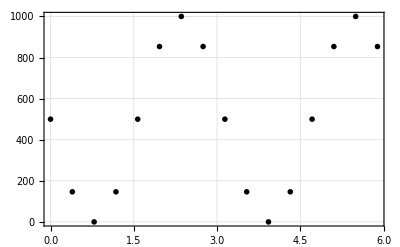

```mathematica
dataPoints=16;
pos=Range[0,2Pi-2Pi/dataPoints,2Pi/dataPoints];
intensity=PolarimeterDataPoint[{{1000},{0},{0},{1000}},0,0,Pi/2,#]&/@pos
op=Partition[Riffle[pos,intensity],2];
ListPlot[{op}]
```

```mathematica
intensity=Map[Around[#,Sqrt[#]]&, intensity]
```

{500.22.,146.12.,0.,146.12.,500.22.,854.29.,1000.32.,854.29.,500.22.,146.12.,0.,146.12.,500.22.,854.29.,1000.32.,854.29.}

```mathematica
DFT[intensity]
```

<|Sin Coefficients→<|0→0.,1→0.8.,2→-500.8.,3→0.8.,4→0.8.,5→0.8.,6→0.8.,7→0.8.,8→0.|>,Cos Coefficients→<|0→500.6.,1→0.8.,2→0.8.,3→0.8.,4→0.8.,5→0.8.,6→0.8.,7→0.8.,8→0.6.|>|>

```mathematica
CalculateStokesFromDFT[DFT[intensity],1,0,0,π/2]
```

<|p0→500.10.,p1→0.0000.032,p2→0.0000.032,p3→1.0000.025|>

Here’s some left circular data

{500.,853.553,1000.,853.553,500.,146.447,0.,146.447,500.,853.553,1000.,853.553,500.,146.447,0.,146.447}

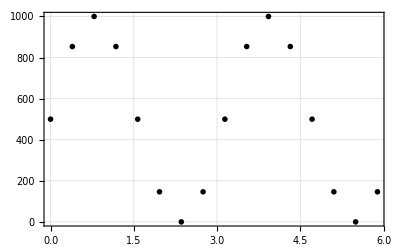

```mathematica
dataPoints=16;
pos=Range[0,2Pi-2Pi/dataPoints,2Pi/dataPoints];
intensity=PolarimeterDataPoint[{{1000},{0},{0},{-1000}},0,0,Pi/2,#]&/@pos
op=Partition[Riffle[pos,intensity],2];
ListPlot[{op}]
```

```mathematica
intensity=Map[Around[#,Sqrt[#]]&, intensity]
```

{500.22.,854.29.,1000.32.,854.29.,500.22.,146.12.,0.,146.12.,500.22.,854.29.,1000.32.,854.29.,500.22.,146.12.,0.,146.12.}

```mathematica
DFT[intensity]
```

<|Sin Coefficients→<|0→0.,1→0.8.,2→500.8.,3→0.8.,4→0.8.,5→0.8.,6→0.8.,7→0.8.,8→0.|>,Cos Coefficients→<|0→500.6.,1→0.8.,2→0.8.,3→0.8.,4→0.8.,5→0.8.,6→0.8.,7→0.8.,8→0.6.|>|>

```mathematica
CalculateStokesFromDFT[DFT[intensity],1,0,0,π/2]
```

<|p0→500.10.,p1→0.0000.032,p2→0.0000.032,p3→-1.0000.025|>

Now we’ll modify where the initial positions of the optical elements are and see if we can account for that.

{961.94,826.641,500.,635.299,961.94,826.641,500.,635.299,961.94,826.641,500.,635.299,961.94,826.641,500.,635.299}

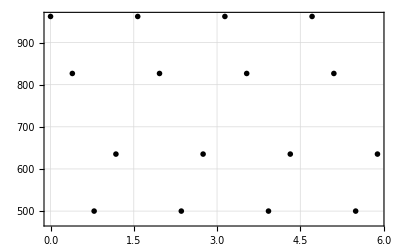

```mathematica
dataPoints=16;
pos=Range[0,2Pi-2Pi/dataPoints,2Pi/dataPoints];
intensity=PolarimeterDataPoint[{{1000},{1000},{0},{0}},Pi/16,0,Pi/2,#]&/@pos
op=Partition[Riffle[pos,intensity],2];
ListPlot[{op}]
```

```mathematica
intensity=Map[Around[#,Sqrt[#]]&, intensity]
```

{962.31.,827.29.,500.22.,635.25.,962.31.,827.29.,500.22.,635.25.,962.31.,827.29.,500.22.,635.25.,962.31.,827.29.,500.22.,635.25.}

```mathematica
DFT[intensity]
```

<|Sin Coefficients→<|0→0.,1→0.10.,2→0.9.,3→0.10.,4→96.10.,5→0.10.,6→0.9.,7→0.10.,8→0.|>,Cos Coefficients→<|0→731.7.,1→0.10.,2→0.10.,3→0.10.,4→231.10.,5→0.10.,6→0.10.,7→0.10.,8→0.7.|>|>

```mathematica
stokes=CalculateStokesFromDFT[DFT[intensity],1,0,0,π/2]
```

<|p0→500.12.,p1→0.920.04,p2→0.380.04,p3→0.0000.018|>

Now I want to see if these stokes parameters are true. p1=.92 and p2 = .38, is that really fully linear light still?

```mathematica
stokes
```

<|p0→500.12.,p1→0.920.04,p2→0.380.04,p3→0.0000.018|>

```mathematica
linearLight=Sqrt[stokes["p1"]^2+stokes["p2"]^2]
```

1.000.04